# Biology 101 - Lesson 03: The Recent Breakthrough

## Willem Nielsen

### Future Directions

So now that we’ve told the Wolframian story of biology, and we’ve gotten a sense for the powerful foundations that have been laid down, you may be wondering, what does the future look like, where can we go from here?

As an indication of the strength of these foundations, Stephen has already made significant progress in applying these ideas to nearby fields.

For instance, he’s done extensive work on the connections between his recent model and machine learning. I won’t get into the details here, but one of the main takeaways is that the ways in which machine learning finds solutions are much like the way biology finds solutions, and therefore a lot of the claims around irreducibility also apply to machine learning models.

Another area that we’ve studied is medicine, and this is the project that I worked with him on. The key idea is to start with an adapted cellular automaton as models for an organism, then apply a perturbation to that automaton (indicated by the arrow):

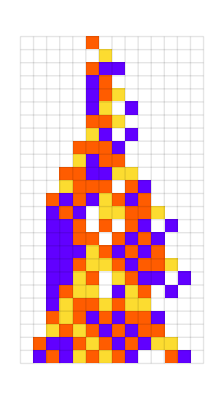
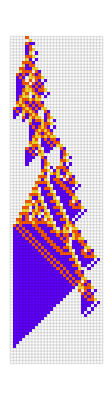
-Graphics--Graphics--Graphics--Graphics-

```mathematica
Row[With[{ru={299459058088077823758143088095350287424,4,1},pt=<|{15,206}->0|>},{{{"[◼]", "PlotCA"}}[ru,"Steps"->24,ImageSize->{Automatic,200},Mesh->All,MeshStyle->Opacity[.1]],{{"[◼]", "PlotCA"}}[ru,"Steps"->105,ImageSize->{Automatic,450},Mesh->All,MeshStyle->Opacity[.1]],Spacer[20],{{"[◼]", "PlotCA"}}[{{"[◼]", "PerturbedCellularAutomaton"}}[ru,{{1},0},{24,{-200,200}},pt],Mesh->All,MeshStyle->Opacity[.1],ImageSize->{Automatic,200}],{{"[◼]", "PlotCA"}}[{{"[◼]", "PerturbedCellularAutomaton"}}[ru,{{1},0},{105,{-200,200}},pt],Mesh->All,MeshStyle->Opacity[.1],ImageSize->{Automatic,450}]}],Spacer[10],Alignment->Bottom]
```

So, we can then study the resulting changes to the pattern as a “metamodel for disease”:

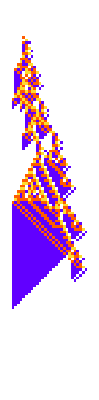
-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-

```mathematica
With[{ru={299459058088077823758143088095350287424,4,1}},Row[Insert[{{"[◼]", "PlotCA"}}[{{"[◼]", "PerturbedCellularAutomaton"}}[ru,{{1},0},{120,{-200,200}},#],ImageSize->{Automatic,330}]&/@{<||>,<|{16,203}->0|>,<|{37,208}->3|>,<|{15,206}->0|>,<|{28,209}->2|>,<|{23,202}->3|>,<|{32,207}->0|>},Spacer[10],2],Spacer[1]]]
```

```mathematica
With[{ru={299459058088077823758143088095350287424,4,1}},GraphicsRow[Insert[{{"[◼]", "PlotCA"}}[{{"[◼]", "PerturbedCellularAutomaton"}}[ru,{{1},0},{120,{-200,200}},#],ImageSize->{Automatic,330}]&/@{<||>,<|{16,203}->0|>,<|{37,208}->3|>,<|{15,206}->0|>,<|{28,209}->2|>,<|{23,202}->3|>,<|{32,207}->0|>},Spacer[10],2]]]
```

-Graphics-

And the important point here is that, because of the irreducibility of the system, even a small change can have a large impact. In the two cases on the right, for example, a single-cell change, led to a very different pattern, with a very different lifetime. Further, because of irreducibility, predicting the changes to the system based on the nature of the perturbation will be computationally challenging.

And this brings us to the fundamental problem of medicine. Given that a perturbation has changed the behavior of the organism in a way that prevents it from achieving it’s goal, which we define here to be having for some finitely long lifetime, can we then “intervene” with a second perturbation, and bring the system back to a “healthy” state:

```mathematica
GraphicsRow[Insert[{{"[◼]", "PlotCA"}}[{{"[◼]", "PerturbedCellularAutomaton"}}[{299459058088077823758143088095350287424,4,1},{{1},0},{120,{-200,200}},#],ImageSize->{Automatic,220}]&/@{<|{23,202}->3|>,<|{23,202}->3,{57,214}->3|>,<|{23,202}->3,{44,209}->2|>,<|{23,202}->3,{34,208}->3|>,<|{23,202}->3,{26,204}->1|>,<|{23,202}->3,{31,202}->3|>,<|{23,202}->3,{35,207}->3|>,<|{23,202}->3,{52,211}->3|>,<||>},Spacer[25],{{2},{-2}}]]
```

-Graphics-

And what we find in general is that a lot of the previously vague, high-level phenomena of medicine, like the importance of early intervention for example, can be concretized in this model.

Going further, in studying the effects of perturbations on adapted systems, we are beginning to formalize when and where “pockets or reducibility” can be found. For instance, we can use a similar setup to the initial adaptive evolution, but instead of selecting purely for “lifetime”, we can select for lifetime under perturbation, as in:

```mathematica
SymIndexMap[k_,r_]:=SymIndexMap[k,r]=With[
{tups=Tuples[Reverse[Range[0,k-1]],2r+1]},
Sort[Catenate[MapIndexed[{Position[tups,#][[1,1]],#2[[1]]}&,
GatherBy[tups,Sort[{#,Reverse[#]}]&],{2}]]]
]
```

```mathematica
SymUp[k_,r_]:=SymUp[k,r
]=SymIndexMap[k,r][[All,2]]
```

```mathematica
SymDown[k_,r_]:=SymDown[k,r
]=Values[KeySort[Map[First,
GroupBy[SymIndexMap[k,r],
Last->First]]]]
```

```mathematica
RandomRuleMutation[{rn_,k_,r_},
many_Integer:1,
OptionsPattern[{"Symmetric"->False}]
]:=Module[
{up,down,cases},
{up,down}=If[
TrueQ[OptionValue["Symmetric"]],
{SymUp[k,r],SymDown[k,r]},
{All,All}
];
cases=IntegerDigits[rn,k,k^(2r+1)][[down]];
{FromDigits[#[[up]],k],k,r}&[
MapAt[Mod[#+RandomInteger[{1,k-1}],k]&,
cases,List/@RandomSample[1;;Length[cases]-1,many]]
] 
]
```

```mathematica
SeedRandom[426778+132];
perts = Reap[bye = NestList[CompoundExpression[
ru=RandomRuleMutation[First[#]],
ca = CellularAutomaton[ru,{{1}, 0}, {200, All}];
lt = {{"[◼]", "TestCALifeTime"}}[ca];
If[lt == -Infinity, #,
(*pcas = Table[PerturbCA[{ca, ru}], Ceiling[lt / 20]];*)
pcas = Table[{{"[◼]", "PerturbedCellularAutomaton"}}[ru,{{1}, 0},{200, {-200, 200}}],5];
Sow[{ru, pcas[[All, 2]]}];
fitness = Min[Join[{lt}, {{"[◼]", "TestCALifeTime"}}/@ pcas]];
If[fitness>=Last[#],{ru,fitness},#]
]]&,{{0,4,1},0},2000]][[2, 1]];
```

```mathematica
kept = Select[perts, MemberQ[bye[[All, 1]],#[[1]]]&] ;
```

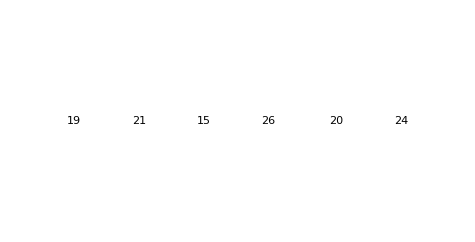

```mathematica
GraphicsRow[Function[{ru, perts}, With[{ca = {{"[◼]", "PerturbedCellularAutomaton"}}[ru, {{1}, 0}, {28,  {-200, 200}}, #]},Labeled[{{"[◼]", "PlotCA"}}[ca, Mesh->True],Text[{{"[◼]", "TestCALifeTime"}}[ca]]]]&/@ Prepend[perts, <||>]]@@kept[[104]]]
```

And the interesting finding, is that in subjecting our “computational organisms” to some noise in their environment, we start to select for more (not complete) reducibility in their mechanisms, here is one particularly reducible automaton that we found, that “uses” a big yellow blade to live a long lifetime despite changes in the environment:

```mathematica
rob = ;
reg = ;
(*See biomedicine-04 for definition*)
```

```mathematica
l1 = Select[rob, {{"[◼]", "TestCALifeTime"}}[CellularAutomaton[#[[1]], {{1}, 0}, 200]]>100&];
```

```mathematica
samplts = ;
```

```mathematica
zd = (samplts /. -Infinity->0);
```

```mathematica
bmi = With[{zd = (samplts /. -Infinity->0)}, 
ReverseSortBy[Range[Length[l1]],Mean[zd[[#]]]&]];
```

```mathematica
l1[[bmi[[1]],1]]
```

{297413941736400589979939780692294751544,4,1}

```mathematica
GraphicsRow[Table[{{"[◼]", "PlotCA"}}[{{"[◼]", "PerturbedCellularAutomaton"}}[{297413941736400589979939780692294751544,4,1},{{1},0},{200,{-200,200}}],"ArrowSize"->Small], 10]]
```

-Graphics-

But what does all this mean?

From following Stephen, and now working with him at the Wolfram Institute, I do believe that we’re having a bit of a “rule-30” moment. Just how before rule-30, there was no clear picture for the origin of complexity from simple systems, I think before Stephen’s recent work, there was no clear picture of an “idealized adaptive system”. And just like how that image of rule-30 eventually allowed Stephen to make broad unifications of various phenomena in different fields of science, I think we now have the potential to do something similar.

It is my hope that, in hearing this story, you can see this potential and are as motivated as I am to make this happen.